(1+r^2)^2-Δr

(3 (-1+r))/r^4

{{r→0.5}}

{30.9839}

{-30.9839}

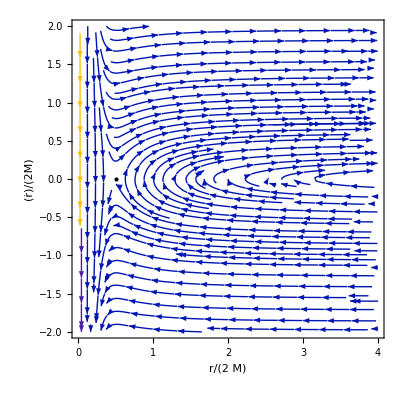

```mathematica
Clear[θ,a,M,m,c,Q,q,Λ,e,L,ρ2,Δr,Δθ,i,R,χ,v,rdot2,rddot,r,sols,sols2,myvars,vars]
θ=Pi/2;
M=1;
a=1;
m=0;
Q=0;
q=0;
Λ=0;
v=0.5;
c=Cos[θ]^2*(a^2*(m^2-e^2)+(L/Sin[θ])^2);
ρ2[r_]=a^2*Cos[θ]^2+r^2;
Δr[r_]=(1-Λ/3*r^2)*(r^2+a^2)-2M*r+Q^2;
Δθ=(1+Λ/3*a^2*Cos[θ]^2);
i=1+Λ/3*a^2;
χ=(a^2+r^2)^2-a^2*Sin[θ]^2*Δr
L=a*e+1;
e=1;
R[r_]=i^2*(e*(r^2+a^2)-a*L+(Q*r*q)/i)^2-Δr[r](c+i^2*(a*e-L)^2+m^2*r^2);
rdot2[r_]=R[r]/ρ2[r]^2;
rddot[r_]=Simplify[1/2*rdot2'[r]]
rdddot[r_]=Simplify[rddot'[r]];
sols=NSolve[rddot[2*M*r]==0,r,Reals]
sols2=Select[r/. sols,Im[#]==0&];
myvars=Array[vars,Length@sols2];
Evaluate@myvars=sols2;
SubPlus[λ]=Simplify[Sqrt[4*rdddot[sols2]]]
SubMinus[λ]=-1*Simplify[Sqrt[4*rdddot[sols2]]]
StreamPlot[{y/(2*M),rddot[2*M*x]/(2*M)},{x,0,4},{y,-2,2},StreamPoints->Fine,AspectRatio->1,Epilog->{PointSize[Large],(Point[{#,0}]&)/@(sols2)},
FrameLabel->{"r/(2  M)",OverDot["r"]/"2M"}]
```